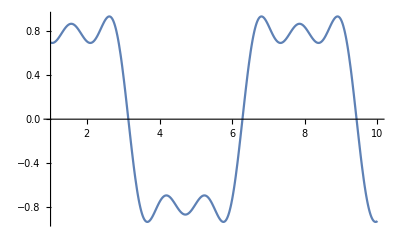

```mathematica
f[t_]:=Sin[t]+(1/3)Sin[3t]+(1/5)Sin[5t]
Plot[f[t],{t,1,10}]
```

c_2

c_1 ω_0+(F ω)/(m (-ω^2+ω_0^2))

{{c_1→-(F ω)/(m ω_0 (-ω^2+ω_0^2)),c_2→0}}

{c_1→-(F ω)/(m ω_0 (-ω^2+ω_0^2)),c_2→0,ω_0→1,ω→2,F→1,m→1}

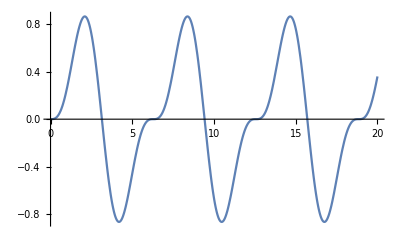

```mathematica
x[t_]:=(F/(m(Subscript[ω, 0]^2-ω^2)))*Sin[ω*t]+Subscript[c, 1]*Sin[Subscript[ω, 0]*t]+Subscript[c, 2]*Cos[Subscript[ω, 0]*t];
x[0]
D[x[t],t]/.t->0
Solve[{x[0]==0,(D[x[t],t]/.t->0)==0},{Subscript[c, 1],Subscript[c, 2]}]
sol=%[[1]]~Join~{Subscript[ω, 0]->1,ω->2,F->1,m->1}
g[t_]:=x[t]/.sol/.sol
Plot[g[t],{t,0,20}]
```

c_2-(F γ)/(m (γ^2+(-ω^2+ω_0^2)^2))

-(γ c_2)/2+Cos[1/2 Arg[-γ^2/4+ω_0^2]] c_1 ((-γ^2/4+ω_0^2)^2)^(1/4)+ⅈ Sin[1/2 Arg[-γ^2/4+ω_0^2]] c_1 ((-γ^2/4+ω_0^2)^2)^(1/4)-(F ω^3)/(m (γ^2+(-ω^2+ω_0^2)^2))+(F ω ω_0^2)/(m (γ^2+(-ω^2+ω_0^2)^2))

{{c_1→-(-F γ^2 √Abs[γ^2-4 ω_0^2]-2 F ω^3 √Abs[γ^2-4 ω_0^2]+2 F ω √Abs[γ^2-4 ω_0^2] ω_0^2)/(m Abs[γ^2-4 ω_0^2] (Cos[1/2 Arg[-γ^2/4+ω_0^2]]+ⅈ Sin[1/2 Arg[-γ^2/4+ω_0^2]]) (γ^2+ω^4-2 ω^2 ω_0^2+ω_0^4)),c_2→(F γ)/(m (γ^2+(-ω^2+ω_0^2)^2))}}

{c_1→-(-F γ^2 √Abs[γ^2-4 ω_0^2]-2 F ω^3 √Abs[γ^2-4 ω_0^2]+2 F ω √Abs[γ^2-4 ω_0^2] ω_0^2)/(m Abs[γ^2-4 ω_0^2] (Cos[1/2 Arg[-γ^2/4+ω_0^2]]+ⅈ Sin[1/2 Arg[-γ^2/4+ω_0^2]]) (γ^2+ω^4-2 ω^2 ω_0^2+ω_0^4)),c_2→(F γ)/(m (γ^2+(-ω^2+ω_0^2)^2)),ω_0→1,ω→2,F→1,m→1,γ→0.5}

0.0540541 ⅇ^(-0.25 t) Cos[0.968246 t]-0.0540541 Cos[2 t]+0.683878 ⅇ^(-0.25 t) Sin[0.968246 t]-0.648649 Cos[t] Sin[t]

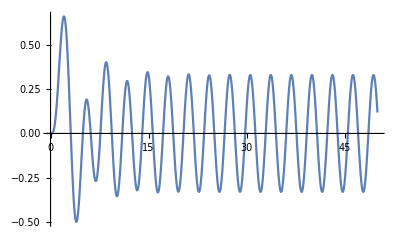

```mathematica
x[t_]:=ComplexExpand[Re[(F/(m((Subscript[ω, 0]^2-ω^2)+I γ)))*Exp[I ω*t-I Pi/2]]+Exp[-(1/2)γ *t](Subscript[c, 1]*Sin[Sqrt[Subscript[ω, 0]^2-γ^2/4]*t]+Subscript[c, 2]*Cos[Sqrt[Subscript[ω, 0]^2-γ^2/4]*t])];
x[0]
D[x[t],t]/.t->0
Solve[{x[0]==0,(D[x[t],t]/.t->0)==0},{Subscript[c, 1],Subscript[c, 2]}]
sol=%[[1]]~Join~{Subscript[ω, 0]->1,ω->2,F->1,m->1,γ->0.5}
g[t_]:=Simplify[x[t]/.sol/.sol,Assumptions->t>0]
g[t]
Plot[FunctionExpand@g[t],{t,0,50}]
```